```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 257 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[q]
q = { r[t] , θ[t] }
```

{r[t],θ[t]}

```mathematica
Clear[s]
s = { r[t] Sin[θ[t]] , r[t] Cos[θ[t]] }
```

{r[t] Sin[θ[t]],Cos[θ[t]] r[t]}

```mathematica
D[s, t]
```

{Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t],Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

r'[t]^2+r[t]^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  )
```

1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
Clear[V]
V = 1/2 k ( r[t]- l)^2- m g r[t] Cos[θ[t]]
```

-g m Cos[θ[t]] r[t]+1/2 k (-l+r[t])^2

```mathematica
Clear[ℒ]
ℒ = T - V
```

g m Cos[θ[t]] r[t]-1/2 k (-l+r[t])^2+1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
D[D[ ℒ , D[q[[1]], t]],t]-D[ℒ,q[[1]]]
D[D[ ℒ , D[q[[2]], t]],t]-D[ℒ,q[[2]]]
```

-g m Cos[θ[t]]+k (-l+r[t])-m r[t] θ'[t]^2+m r''[t]

g m r[t] Sin[θ[t]]+2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]

```mathematica
Table[
D[D[ ℒ , D[q[[i]], t]],t]-D[ℒ,q[[i]]]== 0 ,
{i,1,2}]
```

{-g m Cos[θ[t]]+k (-l+r[t])-m r[t] θ'[t]^2+m r''[t]==0,g m r[t] Sin[θ[t]]+2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]==0}

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

k l+g m Cos[θ[t]]+r[t] (-k+m θ'[t]^2)-m r''[t]==0
-m r[t] (g Sin[θ[t]]+2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
k-> 100,
g-> 9.8,
m -> 2,
l-> 5 
};
parameters // TableForm
```

k→100
g→9.8
m→2
l→5

```mathematica
{{k->100}, {g->9.8}, {m->10}, {l->5}}
```

{k→100,g→9.8,m→10,l→5}

```mathematica
eqs /. parameters
```

{500+19.6 Cos[θ[t]]+r[t] (-100+2 θ'[t]^2)-2 r''[t]==0,-2 r[t] (9.8 Sin[θ[t]]+2 r'[t] θ'[t]+r[t] θ''[t])==0}

```mathematica
Clear[ics]
ics = {
r[0] == 6,
r'[0] == 0,
θ[0] == π/6,
θ'[0] == 0
};
ics // TableForm
```

r[0]==6
r'[0]==0
θ[0]==π/6
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics] , q, {t ,0,300}]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q/. solution[t ] ], {t,0,10} , PlotLabels-> q  ]
```

-Graphics-

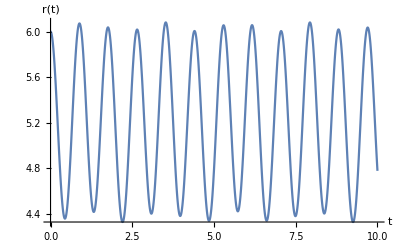

```mathematica
Plot[ Evaluate[ q[[1]]/. solution[t ] ], {t,0,10} ,AxesLabel-> { t , q[[1]] }  ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

r[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0 , tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.1 , 300 } ]
```

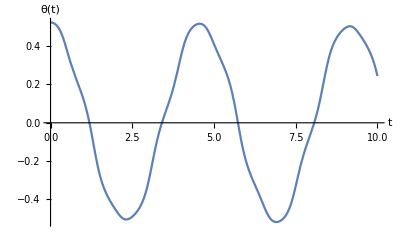

```mathematica
Plot[ Evaluate[ q[[2]]/. solution[t ] ], {t,0,10} ,AxesLabel-> { t , q[[2]] }  ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0 , tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  , { tmax , 0, 300 } ]
```

```mathematica
eqs  // TableForm
```

k l+g m Cos[θ[t]]+r[t] (-k+m θ'[t]^2)-m r''[t]==0
-m r[t] (g Sin[θ[t]]+2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[rReplace]
rReplace = 
Flatten[Solve[ ρ[t] == r[t] -r0 , r[t] ] ]
```

{r[t]→r0+ρ[t]}

```mathematica
D[rReplace, t]
```

{r'[t]→ρ'[t]}

```mathematica
D[D[rReplace, t], t]
```

{r''[t]→ρ''[t]}

```mathematica
eqs /. rReplace /. D[rReplace, t]  /. D[D[rReplace, t], t]  // TableForm
```

k l+g m Cos[θ[t]]+(r0+ρ[t]) (-k+m θ'[t]^2)-m ρ''[t]==0
-m (r0+ρ[t]) (g Sin[θ[t]]+2 θ'[t] ρ'[t]+(r0+ρ[t]) θ''[t])==0

```mathematica
Clear[𝓆]
𝓆 = { ρ[t] , θ[t] }
```

{ρ[t],θ[t]}

```mathematica
Clear[neweqs]
neweqs = 
Normal[ Series[ eqs /. rReplace /. D[rReplace, t]  /. D[D[rReplace, t], t] , { θ[t] , 0 , 1 } ] ] // Expand
```

{k l+g m-k r0-k ρ[t]+m r0 θ'[t]^2+m ρ[t] θ'[t]^2-m ρ''[t]==0,-g m r0 θ[t]-g m θ[t] ρ[t]-2 m r0 θ'[t] ρ'[t]-2 m ρ[t] θ'[t] ρ'[t]-m r0^2 θ''[t]-2 m r0 ρ[t] θ''[t]-m ρ[t]^2 θ''[t]==0}

```mathematica
Length[neweqs[[1,1]]]
```

7

```mathematica
Clear[pieces]
pieces = 
Table[
neweqs[[1,1,i]] ,
{ i , 1 , Length[neweqs[[1,1]]] } ]
```

{k l,g m,-k r0,-k ρ[t],m r0 θ'[t]^2,m ρ[t] θ'[t]^2,-m ρ''[t]}

```mathematica
(* There has to be a way to count the numer of terms *)
```